```mathematica
Clear["@"];
```

Clear::wrsym: Symbol a is Protected.

Clear::wrsym: Symbol b is Protected.

Clear::wrsym: Symbol c is Protected.

General::stop: Further output of Clear will be suppressed during this calculation.

```mathematica
(*SetDirectory["E:\\work\\thesis\\kaiTi\\nb"];data=Import["E:\\work\\thesis\\kaiTi\\标定后的数据\\calib_50.dat","Data"];*)
```

```mathematica
Kernel[x_,y_]=(x.y)^2
```

(x.y)^2

```mathematica
(*aa=Evaluate[ Array[{16Cos[#/32 ℼ],16Sin[#/32 ℼ]}&,{64}]]*)
xx= Map[16Cos[#/32 Pi]&,Range[64]];
yy= Map[16Sin[#/32 Pi]&,Range[64]];
x1= Map[20Cos[#/32 Pi]-4&,Range[64]];
y1= Map[20Sin[#/32 Pi]&,Range[64]];
(*Reap[Do[Print[16*Cos[i/32 ℼ]],{i,64}]]*)
```

```mathematica
ListPlot[{xx,yy}];
```

```mathematica
Join[{xx},{yy}]//MatrixForm;
zz=Transpose[Join[{xx},{yy}]];
z1=Transpose[Join[{x1},{y1}]];
```

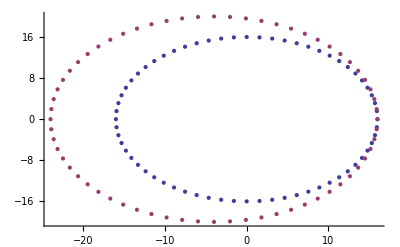

```mathematica
ListPlot[{zz,z1}]
```

```mathematica
X=xx*xx;
Y=√2 yy*yy;
Z=√2 xx*yy;
dd=Transpose[Join[{X},{Y},{Z}]];
dd//MatrixForm;
X1=x1*x1;
Y1=√2 y1*y1;
Z1=√2 x1*y1;
d1=Transpose[Join[{X1},{Y1},{Z1}]];
```

```mathematica
ListPointPlot3D[{dd,d1},BoxRatios->{1,1,1}]
```

-Graphics3D-

#### 1.4 Some typical kernels

Here, we  mention  some typical kernels and display them  in case of X⊂ℝ^1.

1.4.1 The Gaussian RBF universal kernel

The Gaussian Radial Basis Function universal kernel with β>0 and all compact X⊂ℝ^n,

K (x, z) = exp(-β (∥x -z∥)^2)

with β = 0.1

```mathematica
β=0.1;K[x_,z_]:=Exp[-β (x-z) Conjugate[(x-z)]];
```

```mathematica
Plot3D[K[x,z],{x,-10,10},{z,-10,10},ViewPoint->{3.849,6.909,4.295},PlotPoints->{30,30}]
```

-Graphics3D-

Figure 1.  Gaussian RBF universal kernel, with β = 0.1,  in case of   x, z ∈ℝ^1